## Testing fit with two-arguments function

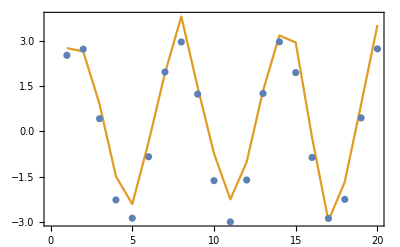

```mathematica
func[x_,a_]:=Sin[x[[1]]]*a+a*x[[2]];
xdata=Table[{i,0},{i,1,20}];
trueData=Map[func[#,3]&,xdata];
fakeData=Table[trueData[[i]]+RandomReal[{-0.2,1}],{i,1,Length[trueData]}];
ListPlot[{trueData,fakeData},Joined->{False, True},Frame->True,Axes->False]
```

```mathematica
NonlinearModelFit[fakeData,func[x,a],{a},{x}]
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{2.76279,2.65477,0.90316,-1.48853,-2.40962,-0.347743,1.93147,3.81367,1.47029,-0.731905,-2.25221,-1.01161,1.34911,3.1845,2.95021,-0.205135,-2.95835,-1.67457,0.900028,3.52856},a x⟦2⟧+a Sin[x⟦1⟧],{a},{x}]